# Yoosook' s Request

## Load Data

```mathematica
GetExperimentID[expStr_]:=ToExpression[#]&/@StringSplit[expStr,"_"][[2;;All]]
SetDirectory["/Volumes/marshallShare/UCI/Yoosook/village/"];
ColorBlend[a_]:=Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},a]
(*Load Data*)
raw=Import["./thresholdCrosses.csv"];
clean=#[[1;;6]]&/@raw;
expTuples={GetExperimentID[#[[1]]],#[[2;;All]]}&/@clean;
paramsRanges=DeleteDuplicates[#]&/@(expTuples[[All,1]]//Transpose)
thresholds={.25,.50,.75,.90,.95};
(* Key: {releaseRatio, releasePattern, fitnessCost, standingVariation}*)
```

{{100,133,200,400,1000,1333,2000,4000,10000,20000,100000,250000,500000,1000000},{1,2,3,4,5,6,7,8,9,10,11,12,13},{100},{1,5,10,50,100,500,1000}}

## Export Response Curves

```mathematica
Table[
trends=Table[
{thresholdIx,releases,standingVar}={5,rel,svar};
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={#[[1,1]]/1000000,#[[2,thresholdIx]]/365}&/@filtered
,{rel,paramsRanges[[2]]}];
linePlot=ListLogPlot[trends
,AspectRatio->1
,Frame->True
(*,FrameLabel->(Style[#,30]&/@{
"Release Fraction", 
"Years to "<>ToString[thresholds[[thresholdIx]]]
})*)
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->None
,FrameTicksStyle->Directive[20]
,GridLines->{Range[0,1,.1],{.1,.2,.5,1,2,5}}
,ImageSize->800
,InterpolationOrder->2
,Joined->True
(*,PlotLabel->Style["Standing Variation: "<>ToString[(standingVar/100000)//N],30]*)
,PlotMarkers->{None, 10}
,PlotRange->{{0,1},{0.05,5}}
,PlotStyle->({Thickness[.006],ColorBlend[#]}&/@Range[0,1,1/Length[paramsRanges[[2]]]])
];
Export[
"./img/CR_"<>"_"<>
StringPadLeft[ToString[Round[thresholds[[thresholdIx]]*1000]],4,"0"]<>
"_"<>StringPadLeft[ToString[standingVar],4,"0"]<>".pdf"
,linePlot
,ImageResolution-> 500
]
,{svar,paramsRanges[[-1]]}]
```

{./img/CR__0950_0001.pdf,./img/CR__0950_0005.pdf,./img/CR__0950_0010.pdf,./img/CR__0950_0050.pdf,./img/CR__0950_0100.pdf,./img/CR__0950_0500.pdf,./img/CR__0950_1000.pdf}

## Export Legend

```mathematica
range=paramsRanges[[2]];
blends=ColorBlend[#]&/@Range[0,1,1/(Length[paramsRanges[[2]]]-1)];
colorScale=Transpose[{
Reverse[ImageResize[Rasterize[#]//ImageCrop,50]&/@blends],
Reverse[Style[ToString[#],35]&/@range]
}]//Grid;
Export["./img/legend.pdf",colorScale]
```

./img/legend.pdf

## Interpolation Function

```mathematica
{thresholdIx,standingVar}={2,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={N[#[[1,1]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
Cases[tuples,{a_,b_,c_}/;c≤12]//Sort
```

{{0.1,4,11.1429},{0.1,5,10.1429},{0.1,6,9.42857},{0.1,7,9.14286},{0.1,8,9.},{0.1,9,9.},{0.1,10,9.},{0.1,11,9.},{0.1,12,9.},{0.1,13,9.},{0.25,2,9.57143},{0.25,3,7.28571},{0.25,4,6.42857},{0.25,5,6.28571},{0.25,6,6.28571},{0.25,7,6.28571},{0.25,8,6.28571},{0.25,9,6.28571},{0.25,10,6.28571},{0.25,11,6.28571},{0.25,12,6.28571},{0.25,13,6.28571},{0.5,1,9.71429},{0.5,2,6.},{0.5,3,5.},{0.5,4,5.},{0.5,5,5.},{0.5,6,5.},{0.5,7,5.},{0.5,8,5.},{0.5,9,5.},{0.5,10,5.},{0.5,11,5.},{0.5,12,5.},{0.5,13,5.},{1.,1,6.42857},{1.,2,4.42857},{1.,3,4.14286},{1.,4,4.14286},{1.,5,4.14286},{1.,6,4.14286},{1.,7,4.14286},{1.,8,4.14286},{1.,9,4.14286},{1.,10,4.14286},{1.,11,4.14286},{1.,12,4.14286},{1.,13,4.14286}}

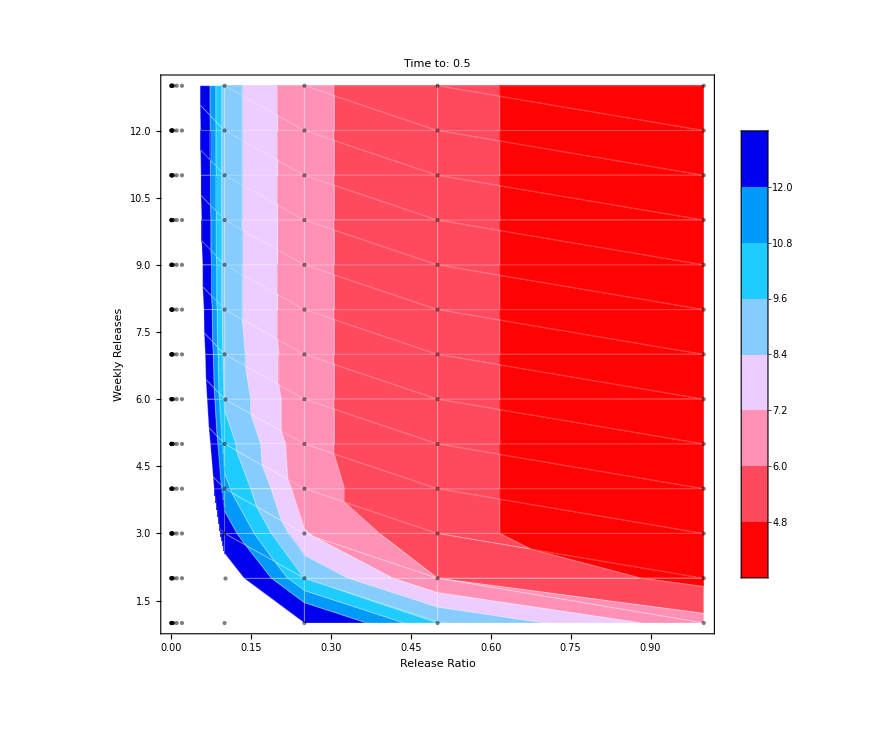

```mathematica
yLabels={paramsRanges[[2]],Round[#]&/@paramsRanges[[2]]}//Transpose;
xLabels={Range[-10,0,3],N[ⅇ^#]&/@Range[-10,0,3]}//Transpose;
ListContourPlot[tuples
,ClippingStyle->White
,ColorFunction->(ColorBlend[#]&)
,ColorFunctionScaling->True
,Contours->10
,Epilog->Flatten[{PointSize[Large],Opacity[.5],(Point[#[[1;;2]]]&/@tuples)}]
,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->{{Automatic,None},{Automatic,None}}
,ImageSize->750
,InterpolationOrder->2
,Mesh->All
,MeshStyle->Directive[ White, Opacity[.25]]
,PlotLabel->Style["Time to: "<>ToString[thresholds[[thresholdIx]]],50,Black]
,PlotLegends->Automatic
,PlotRange->{All,All,{0,14}}
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
```

```mathematica
xLabels
```

{{0.,Indeterminate},{0.2,-1.60944},{0.4,-0.916291},{0.6,-0.510826},{0.8,-0.223144},{1.,0.}}

{{1,0},{2,Log[2]},{3,Log[3]},{4,Log[4]},{5,Log[5]},{6,Log[6]},{7,Log[7]},{8,Log[8]},{9,Log[9]},{10,Log[10]},{11,Log[11]},{12,Log[12]},{13,Log[13]}}

```mathematica
(*ListPlot3D[tuples
,ClippingStyle->White
,ColorFunction->(ColorBlend[#]&)
,ColorFunctionScaling->False
,ImageSize->750
,InterpolationOrder->0
,Mesh->All
,MeshStyle->Directive[Thick, White, Opacity[.25]]
,PlotLegends->Automatic
,PlotRange->{All,All,{0,All}}
,PlotRangePadding->None
,Epilog->Flatten[{PointSize[Medium],(Point[#[[1;;2]]]&/@tuples)}]
]*)
```

```mathematica
pf=Predict[({#[[1]],#[[2]]}->#[[3]])&/@tuples];
```

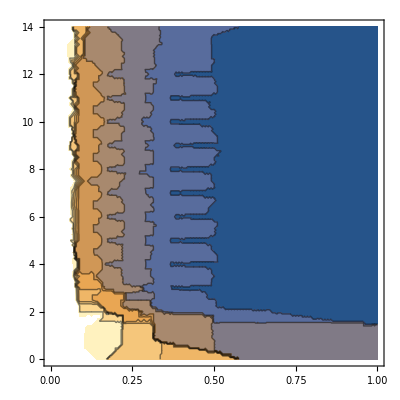

```mathematica
ContourPlot[pf[{a,b}],{a,0,1},{b,0,14}]
```